```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

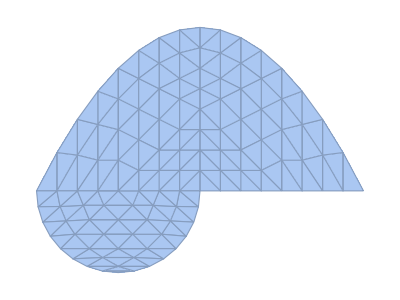

```mathematica
(* import nodes and triangles *)
nodes=Import["nCurve.dat","Table"];
(* Mathematica counts from 1 not 0 *)
triangles=Import["tCurve.dat","Table"]+1;
elements=Triangle/@triangles; (* map Triangles[] at each element of list of triangles *)
𝒦=MeshRegion[nodes,elements]
```

```mathematica
(* unit speed parametrization *)
r⃗[t_]={t-1,-Sqrt[1/4-(t-1/2)^2]};
v⃗[t_]=D[r⃗[t], t];
v[t_]=Norm@v⃗[t];
```

```mathematica
s[t_]=Assuming[0≤t≤1,∫_0^t v[u]ⅆu]
```

Piecewise[{{π/2, t==1}, {ArcSin[√t], 0<t<1}, {0, True}}]

```mathematica
r⃗[(Sin[π/2 t])^2]
```

{-1+Sin[(π t)/2]^2,-√(1/4-(-1/2+Sin[(π t)/2]^2)^2)}